(3 | 1
4 | 1
5 | 2
7 | 3
-5 | -1)

(0.948683 | 0.316228
0.970143 | 0.242536
0.928477 | 0.371391
0.919145 | 0.393919
-0.980581 | -0.196116)

{-0.219388,0.975638}

(0.100394
0.0237893
0.158646
0.182673
0.0237893)

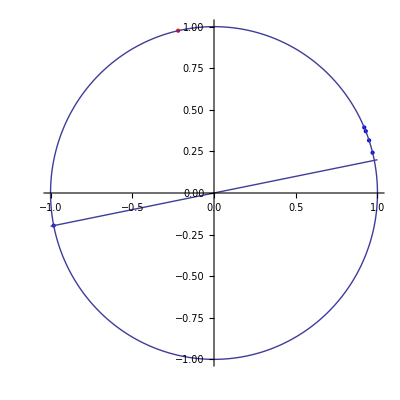

```mathematica
MatrixForm[M = {{3, 1}, {4,1}, {5,2}, {7, 3}, {-5,-1}}]
N[MatrixForm[S = Table[M[[i]]/Norm[M[[i]]], {i, 1, Length[M]}]]]
result = 1;
vN = 1;
theta = 1;
phi = 1;
X = 1;
For[i=1,i<Length[S]+1, i++, 
For[j=i+1,j<Length[S]+1,j++, 
If[S[[i]].S[[j]]==1, Delete[S,j],
If[S[[i]].S[[j]]==-1, result=0]
]
]
]
If[result≠0,
vN = N[(S[[1]]+S[[2]])/Norm[S[[1]]+S[[2]]]];
theta= N[ArcCos[vN.S[[1]]]];
i=3;
While [result≠0&& i<Length[S]+1,
{
phi=N[ArcCos[vN.S[[i]]]];
If[(phi+theta)<Pi,
{
X= N[Sin[phi+theta]/Sin[phi]vN-Sin[theta]/Sin[phi]S[[i]]];
vN = N[(X+S[[i]])/Norm[X+S[[i]]]];
theta=N[(phi +theta)/2];
},
result=0;
]
};
i++;
]
]
If[result≠0,result=vN]
N[MatrixForm[result.Transpose[S]]]
Show[ListPlot[S,PlotStyle->Directive[Blue, Thick,PointSize[Large]]],ListPlot[{result}, PlotStyle->Directive[Red, Thick,PointSize[Large]]], ParametricPlot[{Cos[t], Sin[t]}, {t, 0, 2 π}],Plot[0.2x, {x, -1,1}], PlotRange-> {{-1, 1},{-1,1}}, AspectRatio->1]
```

```mathematica
MatrixForm[M = {{3, 1,3}, {4,1,1}, {5,2,2}, {7, 3,1}, {-2,-1,1}}]
N[MatrixForm[S = Table[M[[i]]/Norm[M[[i]]], {i, 1, Length[M]}]]]
result = 1;
vN = 1;
theta = 1;
phi = 1;
X = 1;
For[i=1,i<Length[S]+1, i++, 
For[j=i+1,j<Length[S]+1,j++, 
If[S[[i]].S[[j]]==1, Delete[S,j],
If[S[[i]].S[[j]]==-1, result=0]
]
]
]
If[result≠0,
vN = N[(S[[1]]+S[[2]])/Norm[S[[1]]+S[[2]]]];
theta= N[ArcCos[vN.S[[1]]]];
i=3;
While [result≠0&& i<Length[S]+1,
{
phi=N[ArcCos[vN.S[[i]]]];
If[(phi+theta)<Pi,
{
X= N[Sin[phi+theta]/Sin[phi]vN-Sin[theta]/Sin[phi]S[[i]]];
vN = N[(X+S[[i]])/Norm[X+S[[i]]]];
theta=N[(phi +theta)/2];
},
result=0;
]
};
i++;
]
]
If[result≠0,Print[result=vN];result.Transpose[S]]//MatrixForm
```

(3 | 1 | 3
4 | 1 | 1
5 | 2 | 2
7 | 3 | 1
-2 | -1 | 1)

(0.688247 | 0.229416 | 0.688247
0.942809 | 0.235702 | 0.235702
0.870388 | 0.348155 | 0.348155
0.911322 | 0.390567 | 0.130189
-0.816497 | -0.408248 | 0.408248)

{0.210267,-0.112865,0.971107}

(0.787184
0.400531
0.481815
0.273967
0.270848)